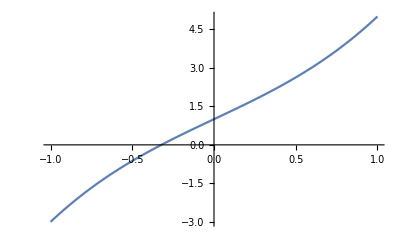

```mathematica
f[x_]:=x^3+3x+1
Plot[f[x],{x,-1,1}]
```

```mathematica
x0=-0.25;
```

```mathematica
h0=-f[x0]/f'[x0]
```

-0.0735294

```mathematica
s0=Interval[x0,x0+2*h0]
```

Interval[{-0.397059,-0.397059},{-0.25,-0.25}]

```mathematica
f'[-0.39705882352941174]*f[-0.39705882352941174]
```

-0.881352

```mathematica
f'[-0.25]*f[-0.25]
```

0.74707

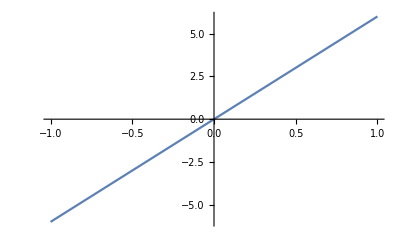

```mathematica
Plot[6x,{x,-1,1}]
```

```mathematica
M=6*(-0.25)
```

-1.5

```mathematica
2*Abs[h0]*M
```

-0.220588

```mathematica
Abs[f'[x0]]
```

3.1875